# The Max-Cut Problem: Variational QAOA

The max-cut problem is to find a partition of vertices in a graph into two complementary sets A and B, such that the number of edges between A and B is as large as possible. Such a cut is said to be the maximum cut of the graph; see Figure 1 below for an example.

-Graphics-

Figure 1. An example of maximum cut. Image at the courtesy of Wikimedia Commons.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

```mathematica
Clear[ParametrizeGraph]
ParametrizeGraph[g,s_?QubitQ]:=
ParametrizeGraph[g,FlavorNone@s]/;Not[FlavorNoneQ@s]
ParametrizeGraph[g_, s_?QubitQ]:=Module[
{vv=VertexList[g],
ee=EdgeList[g]},
vv=Thread[vv->s[Range[Length@vv],$]]
]
```

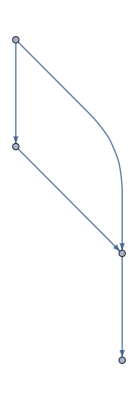

```mathematica
gr=Graph[{1->2,1->3,2->3,3->4}]
```

```mathematica
ParametrizeGraph[gr,S[1]]
```

{1→S_(,,11),2→S_(,,12),3→S_(,,13),4→S_(,,14)}

```mathematica
ee=EdgeList[gr]
```

{1->2,1->3,2->3,3->4}

```mathematica
DisjointQ[ee[[1]],ee[[4]]]
```

True

```mathematica
S[3,$][4,$]
```

S_(,,34)

```mathematica
S[3,$][{1,2,3},$]
```

{S_(,,31),S_(,,32),S_(,,33)}